# Лабораторная работа №4

## Лабораторная работа №4. Mathematica. Общие правила работы с графикой.

## 1

### 1

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat=(ymax-ymin)/(xmax-xmin);
fXY[x_,y_]:=2-E^(-(x/2-2)^2-(y-2)^2)+2 E^(-(x/2-3)^2-(y/3-1)^2);
```

## 2

### 2.a

Что следует вписать вместо Yaaaa для получения показанного ниже графика?
-Graphics-

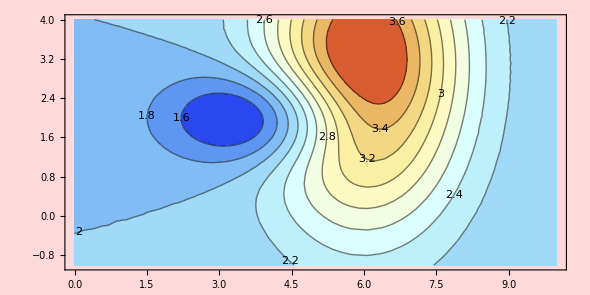

```mathematica
grf2Db=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRangePadding->{{1,4},{0,2}},Background->LightRed]
```

### 2.b

Что следует вписать вместо Ybbbb для получения показанного ниже графика?
-Graphics-
-Graphics-

```mathematica
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRegion->{{0.3,1},{0,0.8}},Background->LightRed]
```

-Graphics-

### 1.c

Что следует вписать вместо Ycccc для получения показанного ниже графика?
-Graphics-
-Graphics-

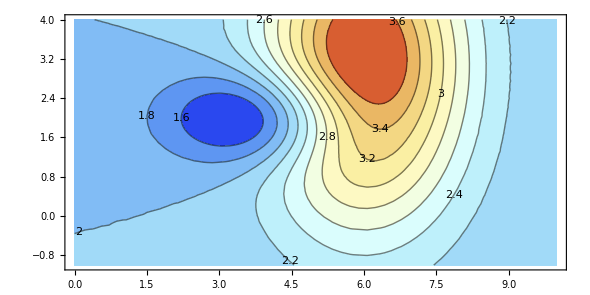

```mathematica
grf2D=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590];
```

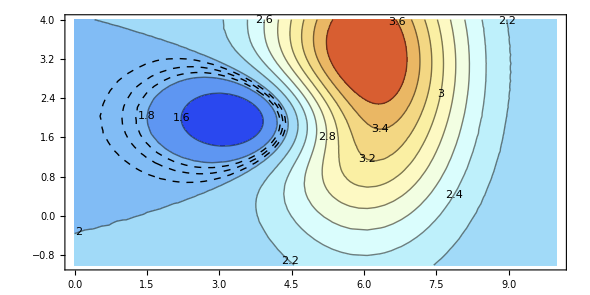

```mathematica
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->{1.85,1.9,1.95},ContourStyle->Dashed,ContourShading->None,AspectRatio->aspRat,ImageSize->590];
Show[grf2D,grf2Dc]
```

### 1.d

Что следует вписать вместо Ydddd для получения показанных ниже графиков?
-Graphics-

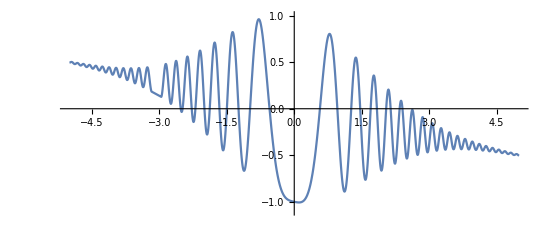

```mathematica
f3[x_]:=(-E^(-0.2 x^2)) Cos[5 x^2]-0.1 x;
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},AspectRatio->3/7,Epilog->Inset[grf1DdFrgm,Scaled[{0.05,.05}],Scaled[{0,0}],4],PlotRange->{-1.1,1},PlotRangeClipping->False,ImageSize->550]
```

### 1.e

Что следует вписать вместо Yeeee для получения показанного ниже графика справа?
-Graphics-

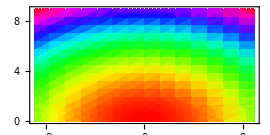
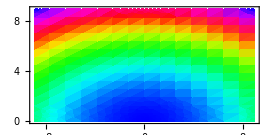

```mathematica
grf2Dd=DensityPlot[x^2+3 y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction->Hue,ImageSize->270];
grf2De=DensityPlot[x^2+3 y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction->(Hue[2/3-#]&),ImageSize->270];
Row[{grf2Dd,grf2De},Spacer[5]]
```